```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/inhomo/MF_DR/renorm_finitep_v2/quakr_prop/Zpsi_normal

```mathematica
Zpsidata=Table[Flatten[Import["./T"<>ToString[i]<>"/Zpsi.dat"]],{i,10,250,20}];
```

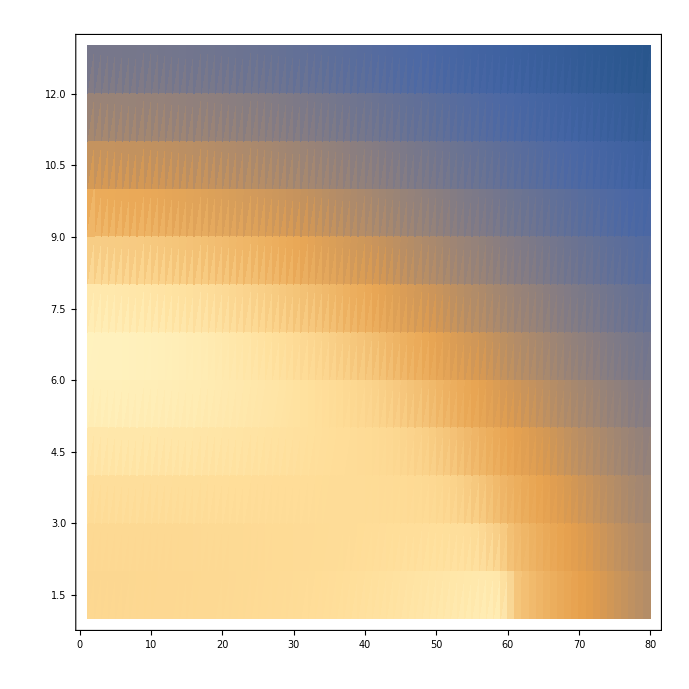

```mathematica
ListDensityPlot[Zpsidata]
```

```mathematica
Export["Zpsidata.dat",Zpsidata]
```

Zpsidata.dat